# Output: MCMLpar

```mathematica
countDat = Import[NotebookDirectory[],"MCMLparOutput.csv"]; (* Edit here! *)
```

```mathematica
dataY = Part[countDat,3;;Length[countDat]];
```

```mathematica
dataXandY = Table[{N[(j)*180/(Length[dataY]-3)],dataY⟦j,1⟧},{j,Length[dataY]-3}];
```

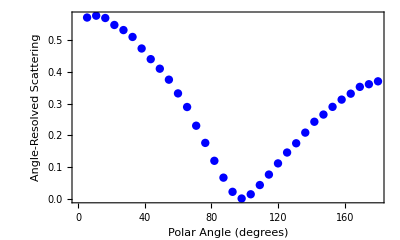

```mathematica
ars = ListPlot[dataXandY,AspectRatio->0.6,PlotStyle-> {Blue,PointSize[0.015]},Frame-> True,FrameStyle->Directive[Thick,Black,Bold,12],FrameLabel-> {"Polar Angle (degrees)","Angle-Resolved Scattering"}]
```